{Cos[0.829156 t]-0.301511 Sin[0.829156 t],Cos[0.829156 t]+0.904534 Sin[0.829156 t]}

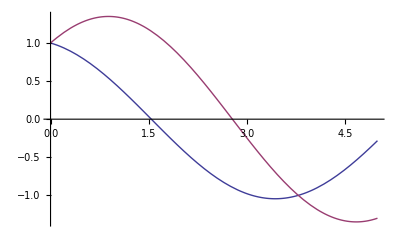

```mathematica
{f[t_],g[t_]}={y[t],x[t]}/.DSolve[{x'[t]==-x[t]/2+5/4 y[t],y'[t]==-3/4 x[t]+y[t]/2,y[0]==1,x[0]==1},{y[t],x[t]},t][[1]]//Expand//N//Chop
Plot[{f[t],g[t]},{t,0,5}]
```